```mathematica
SetDirectory["/Users/claireplunkett/Documents/REU/MAR Results"];
```

```mathematica
RDataImport[folder_,covariates_]:=Module[{a,b,c,dim,m},
b=Import[folder <> "/bestfit.B.csv"];
dim = Sqrt[Dimensions[b][[1]]-1];
b=Partition[b[[2;;-1,3]],dim];
a = Import[folder <> "/bestfit.A.csv"];
a = a[[All,2]];
If[covariates==0,
m = Transpose[Join[{a},b]];,
c = Import[folder <> "/bestfit.C.csv"];
c = Partition[Flatten[c[[2;;-1,3]]],dim];
m=Transpose[Join[{a},c,b]];
];
m
]
RBootImport[folder_,covariates_]:=Module[{a,b,c,dim,m},
b=Import[folder <> "/bootstrap.B.csv"];
dim = Sqrt[Dimensions[b][[1]]-1];
b=Partition[b[[2;;-1,3]],dim];
a = Import[folder <> "/bootstrap.A.csv"];
a = a[[All,2]];
If[covariates==0,
m = Transpose[Join[{a},b]];,
c = Import[folder <> "/bootstrap.C.csv"];
c = Partition[Flatten[c[[2;;-1,3]]],dim];
m=Transpose[Join[{a},c,b]];
];
m
]
```

```mathematica
Remove[size];
For[i=1,i≤17,i++,
mR[i]=RDataImport[ToString[i],0];
size[i]=Dimensions[mR[i]][[2]];
bR[i]=mR[i][[All,2;;size[i]]];
]
For[i=18,i≤31,i++,
mR[i]=RDataImport[ToString[i],1];
size[i]=Dimensions[mR[i]][[2]];
bR[i]=mR[i][[All,3;;size[i]]];
]
For[i=32,i≤33,i++,
mR[i]=RDataImport[ToString[i],2];
size[i]=Dimensions[mR[i]][[2]];
bR[i]=mR[i][[All,4;;size[i]]];
]
```

```mathematica
Remove[size];
For[i=1,i≤17,i++,
mRb[i]=RBootImport[ToString[i],0];
size[i]=Dimensions[mRb[i]][[2]];
bRb[i]=mRb[i][[All,2;;size[i]]];
]
For[i=18,i≤31,i++,
mRb[i]=RBootImport[ToString[i],1];
size[i]=Dimensions[mRb[i]][[2]];
bRb[i]=mRb[i][[All,3;;size[i]]];
]
For[i=32,i≤33,i++,
mRb[i]=RBootImport[ToString[i],2];
size[i]=Dimensions[mRb[i]][[2]];
bRb[i]=mRb[i][[All,4;;size[i]]];
]
```

```mathematica
(bRb[#]//MatrixForm)&/@Range[33]
```

{(0.711756 | -0.33834 | 0
0 | 0.783196 | 0
0 | 0.610155 | 0),(0.669891 | 0 | -0.337935 | 0
-0.101546 | 0.464079 | -0.429538 | 0
0 | -0.143888 | 0.599791 | 0
0 | 0 | 0 | 0.517258),(0.778358 | 0 | -0.295929 | 0
0 | 0.823325 | 0 | 0
0 | -0.104095 | 0.716497 | 0
0 | -0.163262 | 0.455432 | 0),(0.68065 | 0 | 0
-0.21097 | 0.56199 | 0
0 | 0 | 0.502303),(0.782495 | -0.158493 | 0.134352 | 0
0.145959 | 0.623965 | 0 | 0
-0.112705 | -0.181518 | 0.473517 | 0.0556914
-0.297901 | -0.325692 | 0 | 0.527218),(0.944737 | 0 | 0
-0.0848225 | 0.753839 | 0
-0.208125 | 0.458071 | 0.141605),(0.768433 | 0.124619 | 0 | 0.165297 | 0 | 0
0 | 0.720673 | -0.212226 | 0 | 0 | 0
0 | 0 | 0.660757 | 0 | 0 | 0
0 | 0 | 0 | 0.712903 | 0 | 0
0 | 0 | -0.127133 | 0 | 0.538535 | 0
0.198701 | 0 | -0.329496 | 0 | 0 | 0.465942),(0.82209 | 0 | 0 | 0 | 0
0 | 0.779981 | 0 | 0 | 0
0 | 0 | 0.699012 | 0 | 0
-0.0782056 | -0.111651 | 0 | 0.634831 | 0
0 | 0 | 0.131314 | 0 | 0.532704),(0.675524 | 0 | -0.29613 | 0
0 | 0.770406 | 0 | 0
0 | 0 | 0.896679 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0.159906
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.7157 | 0 | 0 | -0.401977 | 0
-0.158499 | 0.423359 | 0 | 0 | -0.0820389
0 | 0 | 0.692734 | 0 | 0
0 | -0.142547 | 0 | 0.865227 | 0
0 | -0.285705 | 0 | 0 | 0.563539),(0 | 0 | 0 | -0.616927 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0.927611 | -0.0822651 | 0
0 | 0 | 0 | 0.73526 | 0
0 | 0 | 1.47788 | 0 | 0),(0.675093 | 0.225652 | 0 | 0
0 | 0.761982 | 0 | 0
0 | 0 | 0.752271 | 0
0 | 0 | 0.52089 | 0),(0.798609 | 0 | 0 | -0.284424 | 0
0.166497 | 0.698434 | -0.263154 | 0 | 0
0.182485 | -0.118337 | 0.572798 | 0 | 0
0 | -0.0475643 | 0 | 0.787288 | 0
0.145077 | 0 | -0.150009 | 0.371859 | 0.467522),(0.767855 | 0 | 0 | -0.229283 | -0.265916 | 0
0 | 0.724524 | 0 | -0.22097 | 0 | 0
0 | 0 | 0.606218 | 0 | -0.11128 | 0
0 | 0 | 0 | 0.523696 | -0.145033 | 0
0 | 0 | 0 | 0 | 0.676265 | 0
0 | 0 | 0 | 0 | 0 | 0.609293),(0.661863 | 0 | 0 | 0 | 0 | -0.237861 | 0
0 | 0.665758 | 0 | -0.301638 | 0.191493 | 0 | 0
0 | 0 | 0.606218 | 0 | 0 | -0.11128 | 0
0 | 0 | 0 | 0.523696 | 0 | -0.145033 | 0
0 | 0.0997923 | -0.143884 | 0 | 0.600219 | 0 | 0
0 | 0 | -0.0664095 | 0 | 0 | 0.629002 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.609293),(0.610505 | 0.544758 | -0.41125 | 0 | 0
0.50299 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | -0.0387938 | 0 | 0.758746 | 0
0 | -0.291615 | 0 | 0 | 0),(0.711756 | -0.33834 | 0
0 | 0.783196 | 0
0 | 0.610155 | 0),(0.669891 | 0 | -0.337935 | 0
0 | 0.486747 | -0.299631 | 0
0 | -0.143888 | 0.599791 | 0
0 | 0 | 0 | 0.517258),(0.778358 | 0 | -0.295929 | 0
0 | 0.823325 | 0 | 0
0 | -0.104095 | 0.716497 | 0
0.0991775 | -0.187052 | 0.528075 | 0),(0.68065 | 0 | 0
-0.21097 | 0.56199 | 0
0 | 0 | 0.502303),(0.782495 | -0.158493 | 0.134352 | 0
0.145959 | 0.623965 | 0 | 0
-0.112705 | -0.181518 | 0.473517 | 0.0556914
-0.297901 | -0.325692 | 0 | 0.527218),(0.944737 | 0 | 0
-0.0848225 | 0.753839 | 0
-0.224174 | 0.572571 | 0),(0.798782 | 0 | 0 | 0.140818 | 0 | 0
0 | 0.720673 | -0.212226 | 0 | 0 | 0
0 | 0 | 0.660757 | 0 | 0 | 0
0 | 0 | 0 | 0.712903 | 0 | 0
0 | 0 | -0.127133 | 0 | 0.538535 | 0
0 | 0 | -0.320774 | 0 | 0 | 0.522129),(0.82209 | 0 | 0 | 0 | 0
0 | 0.779981 | 0 | 0 | 0
0 | 0 | 0.699012 | 0 | 0
-0.0782056 | -0.111651 | 0 | 0.634831 | 0
-0.228813 | 0 | 0.187213 | 0 | 0.478428),(0.833527 | 0 | 0 | 0
0 | 0.770406 | 0 | 0
0 | 0.0965048 | 0.818756 | 0
0 | 0.451226 | 0 | 0),(0 | 0 | 0 | 0.159906
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0.764591),(0.7157 | 0 | 0 | -0.401977 | 0
-0.158499 | 0.423359 | 0 | 0 | -0.0820389
0 | 0 | 0.706471 | 0 | -0.0665298
0 | -0.142547 | 0 | 0.865227 | 0
0 | -0.297663 | 0 | 0.174375 | 0.516044),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0.927611 | -0.0822651 | 0
0 | 0 | 0 | 0.73526 | 0
0 | 0 | 1.47788 | 0 | 0),(0.675093 | 0.225652 | 0 | 0
0 | 0.761982 | 0 | 0
-0.0225912 | 0 | 0.732118 | 0
0 | 0 | 0.52089 | 0),(0.798609 | 0 | 0 | -0.284424 | 0
0.16677 | 0.703259 | -0.26154 | 0 | 0.0947933
0.182485 | -0.118337 | 0.572798 | 0 | 0
0 | -0.0475643 | 0 | 0.787288 | 0
0.0561049 | 0 | 0 | 0.327418 | 0.482207),(0.661863 | 0 | 0 | 0 | -0.237861 | 0
0 | 0.526827 | 0 | 0 | 0 | 0
0 | 0 | 0.631408 | 0 | 0 | 0
0 | 0 | -0.135408 | 0.591218 | -0.197123 | 0
0 | 0 | 0 | 0 | 0.676265 | 0
0 | 0 | 0 | 0 | 0 | 0.609293),(0.661863 | 0 | 0 | 0 | 0 | -0.237861 | 0
0 | 0.582299 | 0 | -0.253283 | 0.153636 | 0 | 0
0 | 0 | 0.631408 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.546466 | 0 | 0 | 0
0 | 0 | -0.110413 | 0 | 0.646337 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.676265 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.609293)}

## Confidence Intervals

```mathematica
RConfidenceIntervalImport[folder_,covariates_]:=Module[{intervalAraw,intervalBraw,intervalCraw,intervalAlow,intervalBlow,intervalClow,intervalAhigh,intervalBhigh,intervalChigh,mlow,mhigh},
intervalAraw=Import[folder<>"/bootstrap.limits.A.csv"];
intervalAlow=intervalAraw[[2;;-1,2]];
intervalAhigh=intervalAraw[[2;;-1,3]];
intervalBraw=Import[folder<>"/bootstrap.limits.B.csv"];
intervalBlow=Partition[intervalBraw[[2;;-1,3]],Sqrt[Dimensions[intervalBraw][[1]]-1]];
intervalBhigh=Partition[intervalBraw[[2;;-1,4]],Sqrt[Dimensions[intervalBraw][[1]]-1]];

If[covariates==0,
mlow = Transpose[Join[{intervalAlow},intervalBlow]];
mhigh=Transpose[Join[{intervalAhigh},intervalBhigh]];,

intervalCraw=Import[folder<>"/bootstrap.limits.C.csv"];
intervalClow=Partition[Flatten[intervalCraw[[2;;-1,3]]],Sqrt[Dimensions[intervalBraw][[1]]-1]];
intervalChigh=Partition[Flatten[intervalCraw[[2;;-1,4]]],Sqrt[Dimensions[intervalBraw][[1]]-1]];
mlow=Transpose[Join[{intervalAlow},intervalClow,intervalBlow]];
mhigh=Transpose[Join[{intervalAhigh},intervalChigh,intervalBhigh]];
];
{mlow,mhigh}
]
```

```mathematica
RConfidenceIntervalImport[ToString[1],0][[1]]//MatrixForm
```

(0.896992 | 0.579115 | -0.765905 | -0.122642
0.334981 | -0.0752282 | 0.623958 | -0.14574
-2.11818 | -0.159934 | 0.238421 | -0.124602)

```mathematica
(* 95% confidence interval *)
```

```mathematica
For[i=1,i≤17,i++,
size=Dimensions[mR[i]][[2]];
mRL[i]=RConfidenceIntervalImport[ToString[i],0][[1]];
mRU[i]=RConfidenceIntervalImport[ToString[i],0][[2]];
bRL[i]=mRL[i][[All,2;;size]];
bRU[i]=mRU[i][[All,2;;size]];
]
For[i=18,i≤31,i++,
size=Dimensions[mR[i]][[2]];
mRL[i]=RConfidenceIntervalImport[ToString[i],1][[1]];
mRU[i]=RConfidenceIntervalImport[ToString[i],1][[2]];
bRL[i]=mRL[i][[All,3;;size]];
bRU[i]=mRU[i][[All,3;;size]];
]
For[i=32,i≤33,i++,
size=Dimensions[mR[i]][[2]];
mRL[i]=RConfidenceIntervalImport[ToString[i],2][[1]];
mRU[i]=RConfidenceIntervalImport[ToString[i],2][[2]];
bRL[i]=mRL[i][[All,4;;size]];
bRU[i]=mRU[i][[All,4;;size]];
]
```

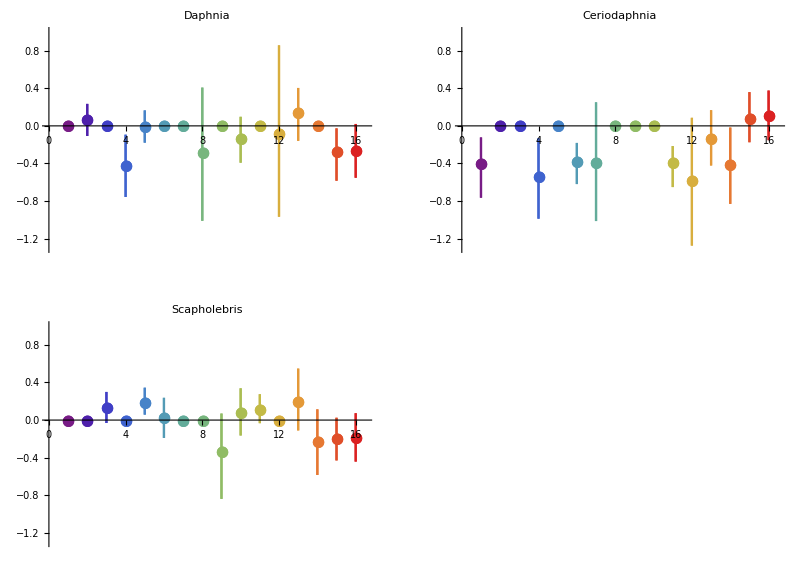

```mathematica
Needs["ErrorBarPlots`"]
cerlist={};cerlistL={};cerlistU={};
daplist={};daplistL={};daplistU={};
scalist={};scalistL={};scalistU={};

For[i=18,i≤33,i++,
size=Dimensions[bb[i]][[1]];
If[MemberQ[rawdata[i][[1]],"Cer_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Cer_ug"],
cerlist=Join[cerlist,{bb[i][[j,size-1]]}];
cerlistL=Join[cerlistL,{bRL[i][[j,size-1]]}];
cerlistU=Join[cerlistU,{bRU[i][[j,size-1]]}];
];
],
cerlist=Join[cerlist,{0}];
cerlistL=Join[cerlistL,{0}];
cerlistU=Join[cerlistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Dapp_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Dapp_ug"],
daplist=Join[daplist,{bb[i][[j,size-1]]}];
daplistL=Join[daplistL,{bRL[i][[j,size-1]]}];
daplistU=Join[daplistU,{bRU[i][[j,size-1]]}];
];
],
daplist=Join[daplist,{0}];
daplistL=Join[daplistL,{0}];
daplistU=Join[daplistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Sca_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Sca_ug"],
scalist=Join[scalist,{bb[i][[j,size-1]]}];
scalistL=Join[scalistL,{bRL[i][[j,size-1]]}];
scalistU=Join[scalistU,{bRU[i][[j,size-1]]}];
];
],
scalist=Join[scalist,{0}];
scalistL=Join[scalistL,{0}];
scalistU=Join[scalistU,{0}];
];

]
cerlist[[{2,3,4,6,7,13,8,10}]]=cerlist[[{4,6,2,3,13,7,10,8}]];
cerlistL[[{2,3,4,6,7,13,8,10}]]=cerlistL[[{4,6,2,3,13,7,10,8}]];
cerlistU[[{2,3,4,6,7,13,8,10}]]=cerlistU[[{4,6,2,3,13,7,10,8}]];
daplist[[{2,3,4,6,7,13,8,10}]]=daplist[[{4,6,2,3,13,7,10,8}]];
daplistL[[{2,3,4,6,7,13,8,10}]]=daplistL[[{4,6,2,3,13,7,10,8}]];
daplistU[[{2,3,4,6,7,13,8,10}]]=daplistU[[{4,6,2,3,13,7,10,8}]];
scalist[[{2,3,4,6,7,13,8,10}]]=scalist[[{4,6,2,3,13,7,10,8}]];
scalistL[[{2,3,4,6,7,13,8,10}]]=scalistL[[{4,6,2,3,13,7,10,8}]];
scalistU[[{2,3,4,6,7,13,8,10}]]=scalistU[[{4,6,2,3,13,7,10,8}]];
daperrorbarlist={};
cererrorbarlist={};
scaerrorbarlist={};
For[i=1,i≤16,i++,
dpoint={{i,daplist[[i]]},ErrorBar[{(daplistL-daplist)[[i]],(daplistU-daplist)[[i]]}]};
daperrorbarlist=Join[daperrorbarlist,{{dpoint}}];
cpoint={{i,cerlist[[i]]},ErrorBar[{(cerlistL-cerlist)[[i]],(cerlistU-cerlist)[[i]]}]};
cererrorbarlist=Join[cererrorbarlist,{{cpoint}}];
spoint={{i,scalist[[i]]},ErrorBar[{(scalistL-scalist)[[i]],(scalistU-scalist)[[i]]}]};
scaerrorbarlist=Join[scaerrorbarlist,{{spoint}}];
]
GraphicsGrid[{{ErrorListPlot[daperrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Daphnia",15]],ErrorListPlot[cererrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Ceriodaphnia",15]]},{ErrorListPlot[scaerrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Scapholebris",15]],PointLegend["Rainbow",{"1 Cer","2 Dap","3 Sca","4 Cer + Dap","5 Dap + Sca","6 Cer + Sca","7 N - Sca - Dap","8 N - Cer - Sca","9 N - Cer - Dap","10 N - Cer","11 N - Dap","12 N - Sca","13 N","14 N + I - Dap","15 N + I","16 N + I + Cop"},LabelStyle->15,LegendMarkerSize->25]}},PlotLabel->Style["Effects of Edible Algae on Herbivores",20],ImageSize->Full]
```

```mathematica
cerlist={};cerlistL={};cerlistU={};
daplist={};daplistL={};daplistU={};
scalist={};scalistL={};scalistU={};

For[i=18,i≤33,i++,
size=Dimensions[bb[i]][[1]];
If[MemberQ[rawdata[i][[1]],"Cer_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Cer_ug"],
cerlist=Join[cerlist,{bb[i][[j,size]]}];
cerlistL=Join[cerlistL,{bRL[i][[j,size]]}];
cerlistU=Join[cerlistU,{bRU[i][[j,size]]}];
];
],
cerlist=Join[cerlist,{0}];
cerlistL=Join[cerlistL,{0}];
cerlistU=Join[cerlistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Dapp_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Dapp_ug"],
daplist=Join[daplist,{bb[i][[j,size]]}];
daplistL=Join[daplistL,{bRL[i][[j,size]]}];
daplistU=Join[daplistU,{bRU[i][[j,size]]}];
];
],
daplist=Join[daplist,{0}];
daplistL=Join[daplistL,{0}];
daplistU=Join[daplistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Sca_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Sca_ug"],
scalist=Join[scalist,{bb[i][[j,size]]}];
scalistL=Join[scalistL,{bRL[i][[j,size]]}];
scalistU=Join[scalistU,{bRU[i][[j,size]]}];
];
],
scalist=Join[scalist,{0}];
scalistL=Join[scalistL,{0}];
scalistU=Join[scalistU,{0}];
];

]
cerlist[[{2,3,4,6,7,13,8,10}]]=cerlist[[{4,6,2,3,13,7,10,8}]];
cerlistL[[{2,3,4,6,7,13,8,10}]]=cerlistL[[{4,6,2,3,13,7,10,8}]];
cerlistU[[{2,3,4,6,7,13,8,10}]]=cerlistU[[{4,6,2,3,13,7,10,8}]];
daplist[[{2,3,4,6,7,13,8,10}]]=daplist[[{4,6,2,3,13,7,10,8}]];
daplistL[[{2,3,4,6,7,13,8,10}]]=daplistL[[{4,6,2,3,13,7,10,8}]];
daplistU[[{2,3,4,6,7,13,8,10}]]=daplistU[[{4,6,2,3,13,7,10,8}]];
scalist[[{2,3,4,6,7,13,8,10}]]=scalist[[{4,6,2,3,13,7,10,8}]];
scalistL[[{2,3,4,6,7,13,8,10}]]=scalistL[[{4,6,2,3,13,7,10,8}]];
scalistU[[{2,3,4,6,7,13,8,10}]]=scalistU[[{4,6,2,3,13,7,10,8}]];
daperrorbarlist={};
cererrorbarlist={};
scaerrorbarlist={};
For[i=1,i≤16,i++,
dpoint={{i,daplist[[i]]},ErrorBar[{(daplistL-daplist)[[i]],(daplistU-daplist)[[i]]}]};
daperrorbarlist=Join[daperrorbarlist,{{dpoint}}];
cpoint={{i,cerlist[[i]]},ErrorBar[{(cerlistL-cerlist)[[i]],(cerlistU-cerlist)[[i]]}]};
cererrorbarlist=Join[cererrorbarlist,{{cpoint}}];
spoint={{i,scalist[[i]]},ErrorBar[{(scalistL-scalist)[[i]],(scalistU-scalist)[[i]]}]};
scaerrorbarlist=Join[scaerrorbarlist,{{spoint}}];
]
GraphicsGrid[{{ErrorListPlot[daperrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Daphnia",15]],ErrorListPlot[cererrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Ceriodaphnia",15]]},{ErrorListPlot[scaerrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Scapholebris",15]],PointLegend["Rainbow",{"1 Cer","2 Dap","3 Sca","4 Cer + Dap","5 Dap + Sca","6 Cer + Sca","7 N - Sca - Dap","8 N - Cer - Sca","9 N - Cer - Dap","10 N - Cer","11 N - Dap","12 N - Sca","13 N","14 N + I - Dap","15 N + I","16 N + I + Cop"},LabelStyle->15,LegendMarkerSize->25]}},PlotLabel->Style["Effects of Inedible Algae on Herbivores",20],ImageSize->Full]
GraphicsGrid[{{ErrorListPlot[daperrorbarlist,PlotRange->{{0,16.5},{-0.5,0.7}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Daphnia",15]],ErrorListPlot[cererrorbarlist,PlotRange->{{0,16.5},{-0.5,0.7}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Ceriodaphnia",15]]},{ErrorListPlot[scaerrorbarlist,PlotRange->{{0,16.5},{-0.5,0.7}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Scapholebris",15]],PointLegend["Rainbow",{"1 Cer","2 Dap","3 Sca","4 Cer + Dap","5 Dap + Sca","6 Cer + Sca","7 N - Sca - Dap","8 N - Cer - Sca","9 N - Cer - Dap","10 N - Cer","11 N - Dap","12 N - Sca","13 N","14 N + I - Dap","15 N + I","16 N + I + Cop"},LabelStyle->15,LegendMarkerSize->25]}},PlotLabel->Style["Effects of Inedible Algae on Herbivores (Adjusted Scale)",20],ImageSize->Full]
```

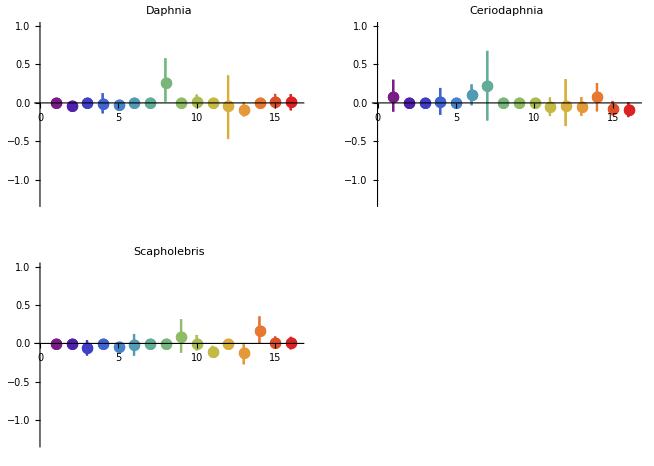

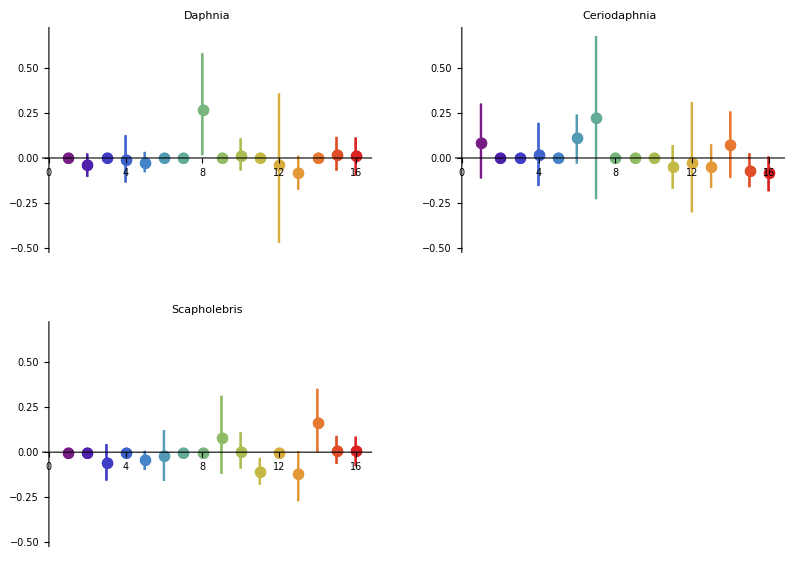

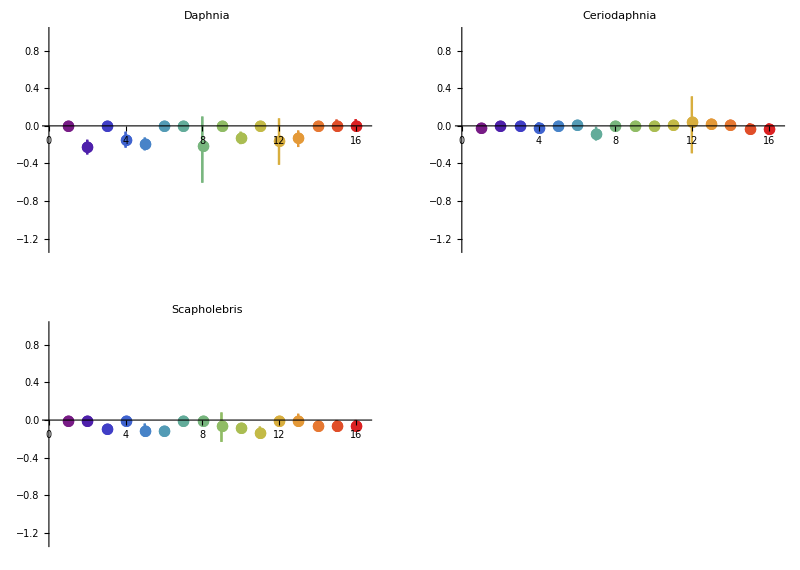

```mathematica
cerlist={};cerlistL={};cerlistU={};
daplist={};daplistL={};daplistU={};
scalist={};scalistL={};scalistU={};

For[i=18,i≤33,i++,
size=Dimensions[bb[i]][[1]];
If[MemberQ[rawdata[i][[1]],"Cer_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Cer_ug"],
cerlist=Join[cerlist,{bb[i][[size-1,j]]}];
cerlistL=Join[cerlistL,{bRL[i][[size-1,j]]}];
cerlistU=Join[cerlistU,{bRU[i][[size-1,j]]}];
];
],
cerlist=Join[cerlist,{0}];
cerlistL=Join[cerlistL,{0}];
cerlistU=Join[cerlistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Dapp_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Dapp_ug"],
daplist=Join[daplist,{bb[i][[size-1,j]]}];
daplistL=Join[daplistL,{bRL[i][[size-1,j]]}];
daplistU=Join[daplistU,{bRU[i][[size-1,j]]}];
];
],
daplist=Join[daplist,{0}];
daplistL=Join[daplistL,{0}];
daplistU=Join[daplistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Sca_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Sca_ug"],
scalist=Join[scalist,{bb[i][[size-1,j]]}];
scalistL=Join[scalistL,{bRL[i][[size-1,j]]}];
scalistU=Join[scalistU,{bRU[i][[size-1,j]]}];
];
],
scalist=Join[scalist,{0}];
scalistL=Join[scalistL,{0}];
scalistU=Join[scalistU,{0}];
];

]
cerlist[[{2,3,4,6,7,13,8,10}]]=cerlist[[{4,6,2,3,13,7,10,8}]];
cerlistL[[{2,3,4,6,7,13,8,10}]]=cerlistL[[{4,6,2,3,13,7,10,8}]];
cerlistU[[{2,3,4,6,7,13,8,10}]]=cerlistU[[{4,6,2,3,13,7,10,8}]];
daplist[[{2,3,4,6,7,13,8,10}]]=daplist[[{4,6,2,3,13,7,10,8}]];
daplistL[[{2,3,4,6,7,13,8,10}]]=daplistL[[{4,6,2,3,13,7,10,8}]];
daplistU[[{2,3,4,6,7,13,8,10}]]=daplistU[[{4,6,2,3,13,7,10,8}]];
scalist[[{2,3,4,6,7,13,8,10}]]=scalist[[{4,6,2,3,13,7,10,8}]];
scalistL[[{2,3,4,6,7,13,8,10}]]=scalistL[[{4,6,2,3,13,7,10,8}]];
scalistU[[{2,3,4,6,7,13,8,10}]]=scalistU[[{4,6,2,3,13,7,10,8}]];
daperrorbarlist={};
cererrorbarlist={};
scaerrorbarlist={};
For[i=1,i≤16,i++,
dpoint={{i,daplist[[i]]},ErrorBar[{(daplistL-daplist)[[i]],(daplistU-daplist)[[i]]}]};
daperrorbarlist=Join[daperrorbarlist,{{dpoint}}];
cpoint={{i,cerlist[[i]]},ErrorBar[{(cerlistL-cerlist)[[i]],(cerlistU-cerlist)[[i]]}]};
cererrorbarlist=Join[cererrorbarlist,{{cpoint}}];
spoint={{i,scalist[[i]]},ErrorBar[{(scalistL-scalist)[[i]],(scalistU-scalist)[[i]]}]};
scaerrorbarlist=Join[scaerrorbarlist,{{spoint}}];
]
GraphicsGrid[{{ErrorListPlot[daperrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Daphnia",15]],ErrorListPlot[cererrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Ceriodaphnia",15]]},{ErrorListPlot[scaerrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Scapholebris",15]],PointLegend["Rainbow",{"1 Cer","2 Dap","3 Sca","4 Cer + Dap","5 Dap + Sca","6 Cer + Sca","7 N - Sca - Dap","8 N - Cer - Sca","9 N - Cer - Dap","10 N - Cer","11 N - Dap","12 N - Sca","13 N","14 N + I - Dap","15 N + I","16 N + I + Cop"},LabelStyle->15,LegendMarkerSize->25]}},PlotLabel->Style["Effects of Herbivores on Edible Algae",20],ImageSize->Full]
GraphicsGrid[{{ErrorListPlot[daperrorbarlist,PlotRange->{{0,16.5},{-0.65,0.4}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Daphnia",15]],ErrorListPlot[cererrorbarlist,PlotRange->{{0,16.5},{-0.65,0.4}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Ceriodaphnia",15]]},{ErrorListPlot[scaerrorbarlist,PlotRange->{{0,16.5},{-0.65,0.4}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Scapholebris",15]],PointLegend["Rainbow",{"1 Cer","2 Dap","3 Sca","4 Cer + Dap","5 Dap + Sca","6 Cer + Sca","7 N - Sca - Dap","8 N - Cer - Sca","9 N - Cer - Dap","10 N - Cer","11 N - Dap","12 N - Sca","13 N","14 N + I - Dap","15 N + I","16 N + I + Cop"},LabelStyle->15,LegendMarkerSize->25]}},PlotLabel->Style["Effects of Herbivores on Edible Algae (Adjusted Scale)",20],ImageSize->Full]
```

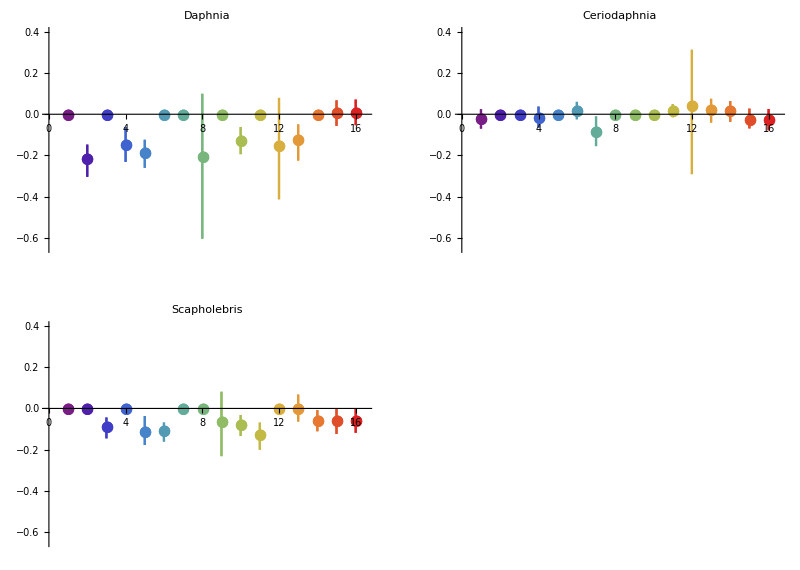

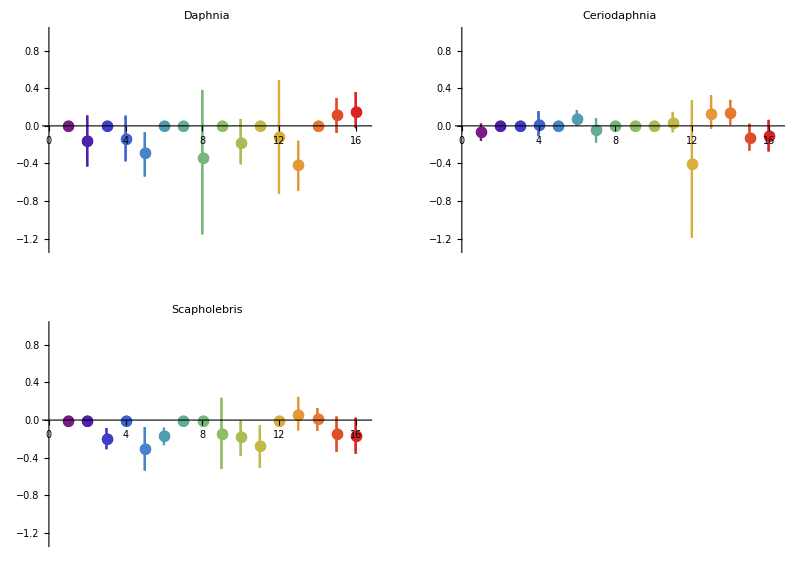

```mathematica
cerlist={};cerlistL={};cerlistU={};
daplist={};daplistL={};daplistU={};
scalist={};scalistL={};scalistU={};

For[i=18,i≤33,i++,
size=Dimensions[bb[i]][[1]];
If[MemberQ[rawdata[i][[1]],"Cer_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Cer_ug"],
cerlist=Join[cerlist,{bb[i][[size,j]]}];
cerlistL=Join[cerlistL,{bRL[i][[size,j]]}];
cerlistU=Join[cerlistU,{bRU[i][[size,j]]}];
];
],
cerlist=Join[cerlist,{0}];
cerlistL=Join[cerlistL,{0}];
cerlistU=Join[cerlistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Dapp_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Dapp_ug"],
daplist=Join[daplist,{bb[i][[size,j]]}];
daplistL=Join[daplistL,{bRL[i][[size,j]]}];
daplistU=Join[daplistU,{bRU[i][[size,j]]}];
];
],
daplist=Join[daplist,{0}];
daplistL=Join[daplistL,{0}];
daplistU=Join[daplistU,{0}];
];

If[MemberQ[rawdata[i][[1]],"Sca_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+2]]=="Sca_ug"],
scalist=Join[scalist,{bb[i][[size,j]]}];
scalistL=Join[scalistL,{bRL[i][[size,j]]}];
scalistU=Join[scalistU,{bRU[i][[size,j]]}];
];
],
scalist=Join[scalist,{0}];
scalistL=Join[scalistL,{0}];
scalistU=Join[scalistU,{0}];
];

]
cerlist[[{2,3,4,6,7,13,8,10}]]=cerlist[[{4,6,2,3,13,7,10,8}]];
cerlistL[[{2,3,4,6,7,13,8,10}]]=cerlistL[[{4,6,2,3,13,7,10,8}]];
cerlistU[[{2,3,4,6,7,13,8,10}]]=cerlistU[[{4,6,2,3,13,7,10,8}]];
daplist[[{2,3,4,6,7,13,8,10}]]=daplist[[{4,6,2,3,13,7,10,8}]];
daplistL[[{2,3,4,6,7,13,8,10}]]=daplistL[[{4,6,2,3,13,7,10,8}]];
daplistU[[{2,3,4,6,7,13,8,10}]]=daplistU[[{4,6,2,3,13,7,10,8}]];
scalist[[{2,3,4,6,7,13,8,10}]]=scalist[[{4,6,2,3,13,7,10,8}]];
scalistL[[{2,3,4,6,7,13,8,10}]]=scalistL[[{4,6,2,3,13,7,10,8}]];
scalistU[[{2,3,4,6,7,13,8,10}]]=scalistU[[{4,6,2,3,13,7,10,8}]];
daperrorbarlist={};
cererrorbarlist={};
scaerrorbarlist={};
For[i=1,i≤16,i++,
dpoint={{i,daplist[[i]]},ErrorBar[{(daplistL-daplist)[[i]],(daplistU-daplist)[[i]]}]};
daperrorbarlist=Join[daperrorbarlist,{{dpoint}}];
cpoint={{i,cerlist[[i]]},ErrorBar[{(cerlistL-cerlist)[[i]],(cerlistU-cerlist)[[i]]}]};
cererrorbarlist=Join[cererrorbarlist,{{cpoint}}];
spoint={{i,scalist[[i]]},ErrorBar[{(scalistL-scalist)[[i]],(scalistU-scalist)[[i]]}]};
scaerrorbarlist=Join[scaerrorbarlist,{{spoint}}];
]
GraphicsGrid[{{ErrorListPlot[daperrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Daphnia",15]],ErrorListPlot[cererrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Ceriodaphnia",15]]},{ErrorListPlot[scaerrorbarlist,PlotRange->{{0,16.5},{-1.3,1}},PlotStyle->"Rainbow",PlotMarkers->{"●",15},PlotLabel->Style["Scapholebris",15]],PointLegend["Rainbow",{"1 Cer","2 Dap","3 Sca","4 Cer + Dap","5 Dap + Sca","6 Cer + Sca","7 N - Sca - Dap","8 N - Cer - Sca","9 N - Cer - Dap","10 N - Cer","11 N - Dap","12 N - Sca","13 N","14 N + I - Dap","15 N + I","16 N + I + Cop"},LabelStyle->15,LegendMarkerSize->25]}},PlotLabel->Style["Effects of Herbivores on Inedible Algae",20],ImageSize->Full]
```

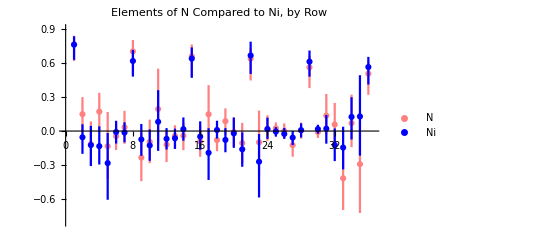

```mathematica
Nerrorbarlist={};
Nierrorbarlist={};
k=1;
For[i=1,i≤ 6,i++,
For[j=1,j≤6,j++,
Npoint={{k,bb[24][[i,j]]},ErrorBar[{(bRL[24]-bb[24])[[i,j]],(bRU[24]-bb[24])[[i,j]]}]};
Nerrorbarlist=Join[Nerrorbarlist,{Npoint}];
Nipoint={{k,bb[32][[i,j]]},ErrorBar[{(bRL[32]-bb[32])[[i,j]],(bRU[32]-bb[32])[[i,j]]}]};
Nierrorbarlist=Join[Nierrorbarlist,{Nipoint}];
k=k+1;
]
]
ErrorListPlot[{Nerrorbarlist,Nierrorbarlist},PlotStyle->{{Pink,Thickness[0.004]},Blue},PlotRange->{{0,36.5},{-0.8,0.9}},PlotLabel->Style["Elements of N Compared to Ni, by Row",20],PlotLegends->{Style["N",20],Style["Ni",20]}]
```

## Work on Covariance

The environmental noise covariance matrix is treated as a set of parameters when calculating the model using a maximum likelihood method, so I expect that each noise covariance matrix from the R covariance files will be a good covariance matrix.

### Test on N-Sca0

```mathematica
VinfRraw[12]=Import["Nsca0" <> "/bestfit.stationary.distribution.covariance.csv"]
```

{{response,predictor,V},{Cer_ug,Cer_ug,17.6458},{Dapp_ug,Cer_ug,20.5155},{Clad_ug,Cer_ug,-28.9168},{e_chl,Cer_ug,-11.3674},{i_chl,Cer_ug,-51.1474},{Cer_ug,Dapp_ug,20.5155},{Dapp_ug,Dapp_ug,28.9732},{Clad_ug,Dapp_ug,-36.9554},{e_chl,Dapp_ug,-14.9283},{i_chl,Dapp_ug,-64.12},{Cer_ug,Clad_ug,-28.9168},{Dapp_ug,Clad_ug,-36.9554},{Clad_ug,Clad_ug,59.0683},{e_chl,Clad_ug,20.9923},{i_chl,Clad_ug,100.508},{Cer_ug,e_chl,-11.3674},{Dapp_ug,e_chl,-14.9283},{Clad_ug,e_chl,20.9923},{e_chl,e_chl,9.12495},{i_chl,e_chl,36.7391},{Cer_ug,i_chl,-51.1474},{Dapp_ug,i_chl,-64.12},{Clad_ug,i_chl,100.508},{e_chl,i_chl,36.7391},{i_chl,i_chl,179.402}}

```mathematica
VinfR[12]=Partition[VinfRraw[12][[2;;-1,3]],5];VinfR[12]//MatrixForm
```

(17.6458 | 20.5155 | -28.9168 | -11.3674 | -51.1474
20.5155 | 28.9732 | -36.9554 | -14.9283 | -64.12
-28.9168 | -36.9554 | 59.0683 | 20.9923 | 100.508
-11.3674 | -14.9283 | 20.9923 | 9.12495 | 36.7391
-51.1474 | -64.12 | 100.508 | 36.7391 | 179.402)

```mathematica
Vinf[12]=Covariance[prodata[12][[1]]];Vinf[12]//MatrixForm
```

(3.26493 | 2.80066 | -0.505828 | -1.34257 | -1.79121
2.80066 | 7.52297 | -2.31415 | -2.71161 | -4.02745
-0.505828 | -2.31415 | 5.01493 | 0.635823 | 6.14213
-1.34257 | -2.71161 | 0.635823 | 2.45175 | 1.62347
-1.79121 | -4.02745 | 6.14213 | 1.62347 | 14.8556)

```mathematica
SigR[12]=Partition[(IdentityMatrix[5^2]-KroneckerProduct[bb[12],bb[12]]).Flatten[VinfR[12]],5]; SigR[12]//MatrixForm
```

(1.97074 | 1.49948 | 0.468738 | -0.0609073 | 0.138463
1.49948 | 3.83641 | 0.387795 | -0.572536 | 0.293457
0.468738 | 0.387795 | 0.687845 | -0.10321 | -0.379009
-0.0609073 | -0.572536 | -0.10321 | 0.565646 | 0.0497371
0.138463 | 0.293457 | -0.379009 | 0.0497371 | 3.95382)

```mathematica
Sig[12]=Partition[(IdentityMatrix[5^2]-KroneckerProduct[bb[12],bb[12]]).Flatten[Vinf[12]],5]; Sig[12]//MatrixForm
```

(1.89819 | 1.5019 | 0.75857 | -0.136008 | 0.572324
1.5019 | 4.06867 | 0.76343 | -0.900648 | 0.72039
0.75857 | 0.76343 | 0.168896 | -0.351459 | -1.38034
-0.136008 | -0.900648 | -0.351459 | 0.958358 | -0.129251
0.572324 | 0.72039 | -1.38034 | -0.129251 | 2.1977)

```mathematica
PositiveSemidefiniteMatrixQ[SigR[12]]
```

True

```mathematica
PositiveSemidefiniteMatrixQ[Sig[12]]
```

False

### Testing All

```mathematica
Remove[size];
For[i=1,i≤17,i++,
VinfRraw[i]=Import[ToString[i]<>"/bestfit.stationary.distribution.covariance.csv"];
size[i]=Sqrt[Dimensions[VinfRraw[i]][[1]]-1];
VinfR[i]=Partition[VinfRraw[i][[2;;-1,3]],size[i]];
SigR[i]=Partition[(IdentityMatrix[size[i]^2]-KroneckerProduct[bR[i],bR[i]]).Flatten[VinfR[i]],size[i]];
]
For[i=18,i≤33,i++,
VinfRraw[i]=Import[ToString[i]<>"/bestfit.stationary.distribution.covariance.csv"];
size[i]=Sqrt[Dimensions[VinfRraw[i]][[1]]-1];
VinfR[i]=Partition[VinfRraw[i][[2;;-1,3]],size[i]];
SigRraw[i]=Import[ToString[i]<>"/bestfit.process.errors.covariance.csv"]; (* R code does not give covariance of covariates *)
SigR[i]=Partition[SigRraw[i][[2;;-1,3]],size[i]];
]
```

```mathematica
VinfR[12]//MatrixForm
```

(17.6458 | 20.5155 | -28.9168 | -11.3674 | -51.1474
20.5155 | 28.9732 | -36.9554 | -14.9283 | -64.12
-28.9168 | -36.9554 | 59.0683 | 20.9923 | 100.508
-11.3674 | -14.9283 | 20.9923 | 9.12495 | 36.7391
-51.1474 | -64.12 | 100.508 | 36.7391 | 179.402)

```mathematica
SigRraw[12]=Import["12/bestfit.process.errors.covariance.csv"];
```

```mathematica
SigRq[12]=Partition[SigRraw[12][[2;;-1,3]],5]//MatrixForm
```

(1.97074 | 1.49948 | 0.468738 | -0.0609073 | 0.138463
1.49948 | 3.83641 | 0.387795 | -0.572536 | 0.293457
0.468738 | 0.387795 | 0.687845 | -0.10321 | -0.379009
-0.0609073 | -0.572536 | -0.10321 | 0.565646 | 0.0497371
0.138463 | 0.293457 | -0.379009 | 0.0497371 | 3.95382)

```mathematica
SigR[12]//MatrixForm
```

(1.97074 | 1.49948 | 0.468738 | -0.0609073 | 0.138463
1.49948 | 3.83641 | 0.387795 | -0.572536 | 0.293457
0.468738 | 0.387795 | 0.687845 | -0.10321 | -0.379009
-0.0609073 | -0.572536 | -0.10321 | 0.565646 | 0.0497371
0.138463 | 0.293457 | -0.379009 | 0.0497371 | 3.95382)

```mathematica
VinfR[19]//MatrixForm
```

(12.6512 | 0.139238 | -1.31143 | -0.316167
0.139238 | 5.52644 | -1.5372 | -2.09396
-1.31143 | -1.5372 | 1.8325 | 1.85404
-0.316167 | -2.09396 | 1.85404 | 7.8402)

```mathematica
bR[19].VinfR[19].Transpose[bR[19]]+(N[Variance[Flatten[prodata[19][[All,All,1]]]]])Outer[Times,mR[19][[All,2]],mR[19][[All,2]]]+SigR[19]//MatrixForm
```

(12.6805 | 0.127608 | -1.30747 | -0.348137
0.127608 | 5.53106 | -1.53877 | -2.08126
-1.30747 | -1.53877 | 1.83303 | 1.84971
-0.348137 | -2.08126 | 1.84971 | 7.87512)

```mathematica
VinfR[21]//MatrixForm
```

(2.78639 | -0.916535 | -1.15603
-0.916535 | 1.45802 | 1.89704
-1.15603 | 1.89704 | 9.38055)

```mathematica
bR[21].VinfR[21].Transpose[bR[21]]+(N[Variance[Flatten[prodata[21][[All,All,1]]]]])Outer[Times,mR[21][[All,2]],mR[21][[All,2]]]+SigR[21]//MatrixForm
```

(2.81078 | -0.913078 | -1.15278
-0.913078 | 1.45851 | 1.8975
-1.15278 | 1.8975 | 9.38098)

```mathematica
VinfR[21]-bR[21].VinfR[21].Transpose[bR[21]]-SigR[21]
```

{{8.88178×10^-16,-9.99201×10^-16,-1.77636×10^-15},{-1.44329×10^-15,6.66134×10^-16,2.66454×10^-15},{-1.55431×10^-15,2.66454×10^-15,0.}}

```mathematica
(N[Variance[Flatten[prodata[21][[All,All,1]]]]])Outer[Times,mR[21][[All,2]],mR[21][[All,2]]]
```

{{0.0243833,0.00345707,0.0032514},{0.00345707,0.000490144,0.000460985},{0.0032514,0.000460985,0.00043356}}

```mathematica
KroneckerProduct[mR[21][[All,2]],mR[21][[All,2]]]//MatrixForm
```

(1.06778 | 0.15139 | 0.142384
0.15139 | 0.0214641 | 0.0201872
0.142384 | 0.0201872 | 0.0189862)

```mathematica
KroneckerProduct[mR[21][[All,2]],IdentityMatrix[1]]//MatrixForm
```

(1.03333
0.146506
0.137791)

```mathematica
Flatten[mR[21][[All,2]]]
```

{1.03333,0.146506,0.137791}

```mathematica
KroneckerProduct[mR[21][[All,2]],mR[21][[All,2]]]//MatrixForm
```

(1.06778 | 0.15139 | 0.142384
0.15139 | 0.0214641 | 0.0201872
0.142384 | 0.0201872 | 0.0189862)

```mathematica
Flatten[KroneckerProduct[mR[21][[All,2]],mR[21][[All,2]]]]
```

{1.06778,0.15139,0.142384,0.15139,0.0214641,0.0201872,0.142384,0.0201872,0.0189862}

```mathematica
mR[32][[All,2;;3]]//MatrixForm
```

(-1.07933 | -0.166521
0.367019 | -1.37002
-0.213958 | -0.468313
-0.286679 | -0.344845
0.167805 | -0.0178264
-0.582485 | -0.211142)

```mathematica
covU[32]=Covariance[Flatten[prodata[32][[All,All,1;;2]],1]]
```

{{0.0256077,0.00225609},{0.00225609,0.188103}}

```mathematica
covU[33]=Covariance[Flatten[prodata[33][[All,All,1;;2]],1]]
```

{{0.0256077,0.00225609},{0.00225609,0.188103}}

```mathematica
m[33]//MatrixForm
```

(7.76181 | -1.07887 | -0.164331 | 0.758048 | -0.0552404 | -0.122897 | -0.133848 | 0.00214487 | -0.281229 | -0.00872858
-0.289474 | 0.406166 | -1.18191 | -0.0435582 | 0.564305 | -0.0308392 | -0.202973 | 0.184242 | 0.106824 | -0.0819468
2.99717 | -0.211253 | -0.455314 | -0.065424 | 0.013054 | 0.639306 | -0.0536145 | 0.0127318 | -0.189133 | 0.00844397
3.97655 | -0.273093 | -0.279563 | -0.0880362 | -0.0384675 | -0.145339 | 0.637355 | 0.0639399 | -0.260352 | 0.0129646
7.38339 | -1.1424 | -0.570486 | -0.0328123 | 0.0796615 | -0.163411 | -0.00190212 | 0.597827 | -0.166497 | 0.0168308
-0.0851883 | 0.168772 | -0.0131783 | -0.0059029 | -0.0264866 | -0.0563872 | 0.00603758 | 0.00455247 | 0.610329 | 0.0171281
3.03015 | -0.59644 | -0.2782 | 0.0317731 | -0.104273 | -0.160414 | 0.151479 | -0.0656788 | 0.119084 | 0.567139)

```mathematica
Partition[Inverse[IdentityMatrix[36]-KroneckerProduct[bb[32],bb[32]]].(KroneckerProduct[mR[32][[All,2;;3]],mR[32][[All,2;;3]]].Flatten[covU[32]]+Flatten[SigR[32]]),6]//MatrixForm
```

(11.4072 | 2.86723 | 1.89456 | 4.43131 | -1.04319 | -0.968026
2.86723 | 6.70609 | 2.5901 | 3.3588 | -0.03435 | -0.443727
1.89456 | 2.5901 | 5.91651 | 3.99904 | -0.824137 | -1.61414
4.43131 | 3.3588 | 3.99904 | 7.17217 | -0.438765 | -0.460523
-1.04319 | -0.03435 | -0.824137 | -0.438765 | 1.42178 | 2.60304
-0.968026 | -0.443727 | -1.61414 | -0.460523 | 2.60304 | 11.3692)

```mathematica
Covariance[prodata[32][[All,All,3;;8]][[1]]]//MatrixForm
```

(5.90804 | 2.82512 | 3.25695 | 5.36558 | -2.07007 | -1.89915
2.82512 | 3.02251 | 1.56537 | 2.81141 | -0.111672 | 0.00710266
3.25695 | 1.56537 | 4.2695 | 2.98419 | -1.48459 | -1.43133
5.36558 | 2.81141 | 2.98419 | 5.73469 | -1.86302 | -1.63686
-2.07007 | -0.111672 | -1.48459 | -1.86302 | 1.82128 | 1.08764
-1.89915 | 0.00710266 | -1.43133 | -1.63686 | 1.08764 | 3.98898)

```mathematica
PositiveSemidefiniteMatrixQ[Partition[Inverse[IdentityMatrix[36]-KroneckerProduct[bb[32],bb[32]]].(KroneckerProduct[mR[32][[All,2;;3]],mR[32][[All,2;;3]]].Flatten[covU[32]]+Flatten[SigR[32]]),6]]
```

True

```mathematica
PositiveSemidefiniteMatrixQ[Partition[Inverse[IdentityMatrix[49]-KroneckerProduct[bb[33],bb[33]]].(KroneckerProduct[mR[33][[All,2;;3]],mR[33][[All,2;;3]]].Flatten[covU[33]]+Flatten[SigR[33]]),7]]
```

True

```mathematica
{#,PositiveSemidefiniteMatrixQ[VinfR[#]]}&/@Range[1,33]//MatrixForm
```

(1 | True
2 | True
3 | True
4 | True
5 | True
6 | True
7 | True
8 | True
9 | True
10 | True
11 | True
12 | True
13 | True
14 | True
15 | True
16 | True
17 | True
18 | True
19 | True
20 | True
21 | True
22 | True
23 | True
24 | True
25 | True
26 | True
27 | True
28 | True
29 | True
30 | True
31 | True
32 | True
33 | True)

```mathematica
{#,PositiveSemidefiniteMatrixQ[SigR[#]]}&/@Range[1,33]//MatrixForm
```

(1 | True
2 | True
3 | True
4 | True
5 | True
6 | True
7 | True
8 | True
9 | True
10 | True
11 | True
12 | True
13 | True
14 | True
15 | True
16 | True
17 | True
18 | True
19 | True
20 | True
21 | True
22 | True
23 | True
24 | True
25 | True
26 | True
27 | True
28 | True
29 | True
30 | True
31 | True
32 | True
33 | True)

```mathematica
bR[24]//MatrixForm
```

(0.762614 | 0.148289 | -0.115393 | 0.170842 | -0.133436 | -0.0451489
0.0329364 | 0.699456 | -0.233406 | -0.0952215 | 0.19302 | -0.119015
-0.043073 | -0.0407375 | 0.655674 | -0.0909997 | 0.147075 | -0.07958
0.0867242 | -0.00843874 | -0.10572 | 0.636192 | -0.0988191 | 0.0160973
0.0231552 | -0.000446728 | -0.124176 | 0.00541699 | 0.559801 | -0.00777701
0.135779 | 0.0571899 | -0.41515 | 0.0693068 | -0.290813 | 0.504101)

```mathematica
bR[32]//MatrixForm
```

(0.758402 | -0.0546454 | -0.123396 | -0.132961 | -0.281524 | -0.00856666
-0.0131503 | 0.615416 | -0.0736551 | -0.12678 | 0.0814729 | -0.0680384
-0.0633227 | 0.016586 | 0.636347 | -0.0483493 | -0.190885 | 0.00940509
-0.0774834 | -0.0207298 | -0.160198 | 0.663797 | -0.26915 | 0.0177913
-0.00515155 | -0.0252237 | -0.0574451 | 0.00792024 | 0.609703 | 0.0174718
0.0209333 | -0.122493 | -0.145151 | 0.124317 | 0.128122 | 0.562181)

## Which Vinf?

```mathematica
math=Covariance[prodata[1][[1]]];math//MatrixForm
```

(5.5157 | -0.472926 | -0.172782
-0.472926 | 0.509476 | 0.429011
-0.172782 | 0.429011 | 4.88786)

```mathematica
PositiveSemidefiniteMatrixQ[math]
```

True

```mathematica
math2={{5,-0.5,-0.1},{-0.5,0.5,0.5},{-0.1,0.5,5}};PositiveSemidefiniteMatrixQ[math2]
math2//MatrixForm
```

True

(5 | -0.5 | -0.1
-0.5 | 0.5 | 0.5
-0.1 | 0.5 | 5)

```mathematica
Covariance[list]//MatrixForm
```

(4.93029 | -0.507992 | -0.171699
-0.507992 | 0.496078 | 0.517857
-0.171699 | 0.517857 | 5.10898)

```mathematica
list=RandomVariate[MultinormalDistribution[{0,0,0},math2],10000]
```

{{-0.876002,0.0584283,-0.24484},{1.97339,-0.844806,-1.36627},{3.67438,-0.915158,-0.105743},{-0.414708,0.838518,0.429962},9993,{-0.832328,0.143255,-0.0705035},{-4.27439,0.707275,0.708189},{-4.19246,0.0869568,1.924}}
 |  |  |  |

```mathematica
Export["testdata_covariance.csv",list]
```

testdata_covariance.csv

```mathematica
Directory[]
```

/Users/claireplunkett/Documents/REU/MAR Results

```mathematica
Covariance[list[[1;;100]]]//MatrixForm
```

(5.15728 | -0.560064 | 0.0618827
-0.560064 | 0.474268 | 0.209098
0.0618827 | 0.209098 | 4.49136)